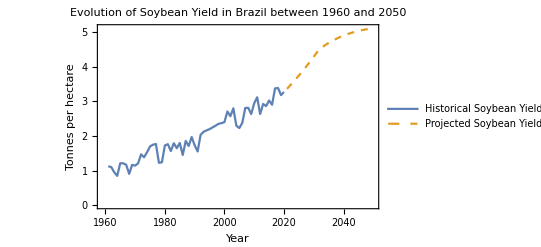

```mathematica
years=Range[1961,2050];
(*The values below come from a dataset of the soybean yield in Brazil from 1961 to 2020 published in OurWorldinData available here: https://ourworldindata.org/soy. *)
historicalSoybeanYield={1.1269,1.1005,0.9503,0.8478,1.2115,1.2125,1.1691,0.9066,1.1661,1.1439,1.2102,1.4705,1.3863,1.5314,1.6985,1.7498,1.7699,1.226,1.2403,1.7273,1.7653,1.5647,1.7921,1.6496,1.8002,1.4522,1.8595,1.7124,1.9714,1.7322,1.5533,2.0352,2.1241,2.1632,2.1998,2.2493,2.2977,2.3533,2.3724,2.4033,2.7105,2.5739,2.8027,2.3005,2.2303,2.3796,2.8133,2.8162,2.6365,2.9475,3.1214,2.6366,2.9285,2.8659,3.0286,2.9049,3.3785,3.3904,3.1847,3.2752};

(* Here we calculate the average annual growth rate of the dataset above, save the last value and define a diminishing factor and a plateau value to predict how the yield of soybeans will increase over the 30 years following the end of the dataset, the values of which we save in a new list*)
averageGrowthRate=Mean[Table[(historicalSoybeanYield[[i+1]]/historicalSoybeanYield[[i]]),{i,Length[historicalSoybeanYield]-1}]];
lastValue=Last[historicalSoybeanYield];

diminishingFactor=0.95;
plateauValue=4.5;

projectedSoybeanYield=Table[Module[{yield},yield=lastValue*averageGrowthRate^i;
If[yield>plateauValue,plateauValue+(yield-plateauValue)*diminishingFactor^i,yield]],{i,30}];

(* We now combine our historical data with our predicted yields and graphically shiw the increase of soybean yields until 2050*)
combinedYield=Join[historicalSoybeanYield,projectedSoybeanYield];

ts=TimeSeries[Transpose[{years,combinedYield}]];

ListLinePlot[{TimeSeriesWindow[ts,{1961,2020}],TimeSeriesWindow[ts,{2021,2050}]},PlotLegends->{"Historical Soybean Yield","Projected Soybean Yield"},Frame->True,FrameLabel->{"Year","Tonnes per hectare"},PlotLabel->"Evolution of Soybean Yield in Brazil between 1960 and 2050",PlotStyle->{Automatic,Dashed}]
```

```mathematica
(* Now we repeat this process for beef production*)



(*From this we can now estimate the total deforestation that would take place until 2050 to meet Chinese demand for soybeans and beef*)
 
deforestedLand=((chineseSoybeanDemand/projectedSoybeanYield)-currentSoybeanLand)*soybeanDeforestationRate+((chineseBeefDemand/projectedBeefYield)-currentBeefLand)*beefDeforestationRate;
 
(*From this we can also estimate the CO2 emissions that would result from this deforestation, taking into account emissions from the beef and soybean sectors as well as from the deforestation*)

emissionsDeforestation = ;
emissionsBeef = ;
emissionsSoybeans = ;
```

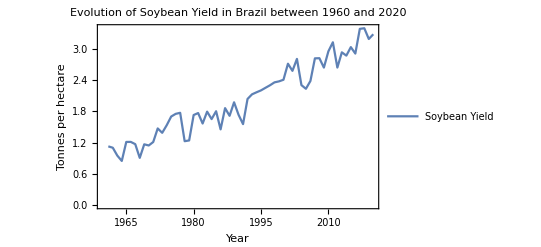

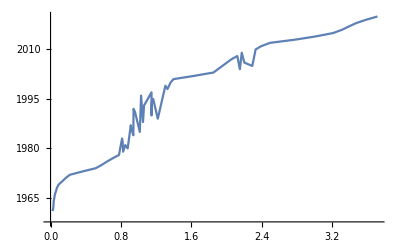

Interpolation::inhr: Requested order is too high; order has been reduced to {1}.

General::stop: Further output of Interpolation::inhr will be suppressed during this calculation.

NDSolve::dsvar: 0 cannot be used as a variable.

ReplaceAll::reps: {50/7-c'[0]==-c[0],1000-c[0]==1000} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 1 cannot be used as a variable.

ReplaceAll::reps: {50/7-c'[1]==50/7-c[1],1000-c[0]==1000} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 2 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {50/7-c'[2]==100/7-c[2],1000-c[0]==1000} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of emissionsAmazon[0].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of emissionsAmazon[1].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of emissionsAmazon[2].

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

-Graphics-

-Graphics-

```mathematica
totalEmissions = emissionsDeforestation+ emissionsBeef + emissionsSoybeans


(*We also want to calulate the output from meeting Chinese demand. We could do this by defining the output as a function dependent on Chinese demand, current output, minus the cost of deforestation (which might be an exponential function since the higher the deforestation the more consequences this has for the economy). A lot more features could be added but this would be relatively simple to start with*)
```